f -функция тока для компонент {v_r(r,z),v_z(r,z)}. Поэтому моды, содержащие только v_ϕ(r,z), не ловятся. При этом первая мода, которая получается не удовлетворяет гран. условиям, поэтому приходится брать со второй.

### Функции

```mathematica
<<ACPackages`
```

```mathematica
v[r_]:=1-r^2;
```

```mathematica
Clear[f,r,k,R]
eqOZ[ω_,k_,R_]:=(v[r]-ω/k)(f''[r]+f'[r]/r-(k^2+1/r^2)f[r])+(v'[r]/r-v''[r])f[r]-ⅈ/(k R)(f''''[r]+2/r f'''[r]-(3/r^2+2 k^2)f''[r]+(3/r^2-2 k^2)(f'[r]/r-f[r]/r^2)+k^4 f[r]);
```

```mathematica
(*КРС с целочисленной сеткой и одинаковыми разностями*)
```

```mathematica
FiniteMatrix4Eigen[n_,sample_:5,subst___]:=Block[{h=1/n,krseq,krs,unk,unkmain,unkfict,i,sm,s,order,lhs,rhs,ω},
sm=Max[sample,5];
unk=Table[Subscript[f, i],{i,0-(sm-1)/2,n+(sm-1)/2}];
unkmain=Table[Subscript[f, i],{i,1,n-1}];
unkfict=Complement[unk,unkmain];dersam[order_,s_]:=Table[Subscript[f, j],{j,i-(s-1)/2,i+(s-1)/2}].NDCoefficientList[order,s]/h^order;
rhs=ω/k(f''[z]-k^2 f[z])/.{z->i h,f[z]->Subscript[f, i],f''[z]->dersam[2,sm],f''''[z]->dersam[4,sm]}/.{subst};
lhs=Simplify[(eqOZ[ω,k,R]+ω/k(f''[z]-k^2 f[z]))]/.{z->i h,f[z]->Subscript[f, i],f''[z]->dersam[2,sm],f''''[z]->dersam[4,sm]}/.{subst};
virfict={Subscript[f, -2]->6 Subscript[f, 0]-8 Subscript[f, 1]+3 Subscript[f, 2],Subscript[f, -1]->3 Subscript[f, 0]-3 Subscript[f, 1]+Subscript[f, 2],Subscript[f, 0]->0,Subscript[f, n]->0,Subscript[f, n+1]->3 Subscript[f, n]-3 Subscript[f, n-1]+Subscript[f, n-2],Subscript[f, n+2]->6 Subscript[f, n]-8 Subscript[f, n-1]+3 Subscript[f, n-2]};
fict=unkfict/.virfict;
rhs=Coefficient[#,unkmain]&/@(Table[rhs,{i,1,n-1}]/.virfict)/ω;
(*Print[rhs//TableForm];*)
lhs=Coefficient[#,unkmain]&/@(Table[lhs,{i,1,n-1}]/.virfict);
(*Print["next:"];
Print[lhs//TableForm];*)
(*Return[rhs.Inverse[lhs]];*)
Return[{lhs,rhs}];
];
```

```mathematica
(*КРС с дробной сеткой и центральными разностями*)
```

```mathematica
FiniteMatrix4Eigen[n_,sample_:5,subst___]:=Block[{h=1/n,krseq,krs,unk,unkmain,unkfict,i,sm,s,order,lhs,rhs,ω},
sm=Max[sample,5];
unk=Table[Subscript[f, i+1/2],{i,0-(sm-1)/2,n+(sm-1)/2-1}];
unkmain=Table[Subscript[f, i],{i,1/2,n-1/2}];
unkfict=Complement[unk,unkmain];
dersam[order_,s_]:=Table[Subscript[f, j],{j,i-(s-1)/2,i+(s-1)/2}].NDCoefficientList[order,s]/h^order;
rhs=-D[eqOZ[ω,k,R],ω]/.{r->i h,f[z_]->Subscript[f, i],f'[z_]->dersam[1,sm],f''[z_]->dersam[2,sm],f'''[z_]->dersam[3,sm],f''''[z_]->dersam[4,sm]}/.{subst};
lhs=Simplify[(eqOZ[ω,k,R]-ω D[eqOZ[ω,k,R],ω])]/.{r->i h,f[z_]->Subscript[f, i],f'[z_]->dersam[1,sm],f''[z_]->dersam[2,sm],f'''[z_]->dersam[3,sm],f''''[z_]->dersam[4,sm]}/.{subst};
virfict=First[Solve[Thread[{dersam[0,sm-1]/.i->0,dersam[1,sm-1]/.i->0,dersam[1,sm-1]/.i->n,dersam[0,sm-1]/.i->n}==0],unkfict]];
fict=unkfict/.virfict;rhs=Coefficient[#,unkmain]&/@(Table[rhs,{i,1/2,n-1/2}]/.virfict);
lhs=Coefficient[#,unkmain]&/@(Table[lhs,{i,1/2,n-1/2}]/.virfict);
(*rhs=Coefficient[#,unk]&/@Join[Table[0,{i,2},{j,n+sm-1}],Table[rhs,{i,1/2,n-1/2}]/ω,Table[0,{i,2},{j,n+sm-1}]];
lhs=Coefficient[#,unk]&/@Join[{dersam[0,sm-1]/.i->0,dersam[1,sm-1]/.i->0},Table[lhs,{i,1/2,n-1/2}],{dersam[1,sm-1]/.i->n,dersam[0,sm-1]/.i->n}];*)
(*Return[rhs.Inverse[lhs]];*)
Return[{lhs,rhs}];
];
```

```mathematica
GetIncrements[n_,k1_,R1_]:=Eigenvalues[Inverse[Last[#]].First[#]&[N[FiniteMatrix4Eigen[n,5,k->k1,R->R1]]]];
```

```mathematica
GetIncrements[n_,k1_,R1_]:=Select[Eigenvalues[N[FiniteMatrix4Eigen[n,5,k->k1,R->R1]]],NumericQ];
```

```mathematica
Take[Sort[GetIncrements[50,1,1],Im[#1]<Im[#2]&],10]
```

{0.999844-21123.3 ⅈ,0.777326+32.607 ⅈ,0.712458+78.7353 ⅈ,0.688317+148.069 ⅈ,0.679095+233.149 ⅈ,0.673398+339.735 ⅈ,0.670538+460.953 ⅈ,0.668272+601.645 ⅈ,0.667027+755.286 ⅈ,0.665845+926.014 ⅈ}

```mathematica
GetMainIncrement[n_,k1_,R1_,num_:2]:=((*Print[R1];*)Take[Sort[Im/@GetIncrements[n,k1,R1]],{num}]//First);
```

```mathematica
GetMainIncrement[20,1,1000,2]
```

0.118595

```mathematica
GetEigenWave[n1_,k1_,R1_,mode_:1]:=Block[{eigval,eigvec,nom,syst},syst=Inverse[Last[#]].First[#]&[N[FiniteMatrix4Eigen[n1,5,k->k1,R->R1]]];
{eigval,eigvec}=Select[Transpose[Eigensystem[syst]],NumericQ[First[#]]&]//Transpose;
nom=Flatten[Position[eigval,Sort[eigval,Im[#1]<Im[#2]&]⟦mode⟧]]//First;
Print["Main eigen value is ",eigval[[nom]]];
Return[eigvec[[nom]]];];
```

```mathematica
GetEigenWave[n1_,k1_,R1_,mode_:1]:=Block[{eigval,eigvec,nom,syst},syst=N[FiniteMatrix4Eigen[n1,5,k->k1,R->R1]];
{eigval,eigvec}=Select[Transpose[Eigensystem[syst]],NumericQ[First[#]]&]//Transpose;
nom=Flatten[Position[eigval,Sort[eigval,Im[#1]<Im[#2]&]⟦mode⟧]]//First;
Print["Main eigen value is ",eigval[[nom]]];
Return[eigvec[[nom]]];];
```

### Проверки

```mathematica
(*Отклонения в определителе после подстановки собственного значения
With[{n2=10,k2=1,R2=10000,mod=1},Det[SetPrecision[First[#]-Sort[GetIncrements[n2,k2,R2],Im[#1]<Im[#2]&][[mod]]Last[#],1000]]&[SetPrecision[FiniteMatrix4Eigen[n2,5,k->k2,R->R2],1000]]]*)
```

```mathematica
(*Отклонения в векторе после подстановки собственных значений и векторов*)
With[{n2=260,k2=1,R2=1000,mod=1},(First[#]-Sort[GetIncrements[n2,k2,R2],Im[#1]<Im[#2]&][[mod]]Last[#]).GetEigenWave[n2,k2,R2,mod]&[FiniteMatrix4Eigen[n2,5,k->k2,R->R2]]]//Abs//PrintRange;
```

$Aborted

### Исследования

```mathematica
Take[incrs,-10]
```

{0.665845+926.014 ⅈ,0.667027+755.286 ⅈ,0.668272+601.645 ⅈ,0.670538+460.953 ⅈ,0.673398+339.735 ⅈ,0.679095+233.149 ⅈ,0.688317+148.069 ⅈ,0.712458+78.7353 ⅈ,0.777326+32.607 ⅈ,0.999844-21123.3 ⅈ}

32.607

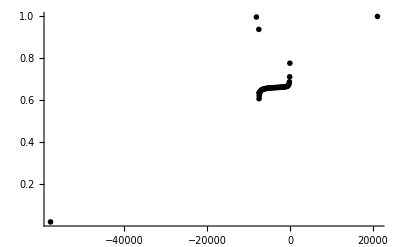

```mathematica
incrs=Sort[N[GetIncrements[50,1,1]],Im[#1]>Im[#2]&];
Print[Im[incrs⟦-2⟧]];
Show[Graphics[{PointSize[0.01],(Point[{-Im[#1],Re[#1]}]&)/@incrs}],Axes->True,PlotRange->{Automatic,Automatic},AspectRatio->1/GoldenRatio]
```

```mathematica
ShowPlot[-GetMainIncrement[100,1,#,2]&,{1,1000}]
```

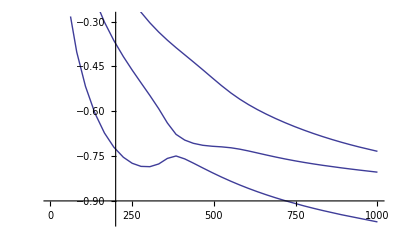
```mathematica
first3log=-Graphics-;
```

```mathematica
Sort[GetIncrements[300,1.,10000],Im[#1]<Im[#2]&]
```

Main eigen value is 0.00078109+0.0324412 ⅈ

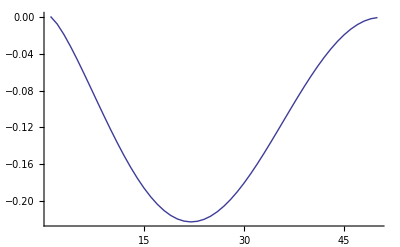
{0.28,-Graphics-}

```mathematica
Timing[PrintRange[WithoutFict[ew=Re/@GetEigenWave[50,0.001,1000,2],0]]]
```

```mathematica
Block[{ew=Re/@GetEigenWave[10,1,1,1],fs},
fs=fict/.{Subscript[f, b_]:>ew[[b+1/2]]};
gr=PrintRange[alllist=Join[Take[fs,Length[fs]/2],ew,Take[fs,-Length[fs]/2]]];
];
```

```mathematica
Plot[Im[GetMainIncrement[10,1,R]],{R,1,20000}]
```

```mathematica
linc=Table[{R,GetMainIncrement[300,1,R]},{R,1,20001,100}];
```

```mathematica
ListPlot[linc]
```

```mathematica
Timing[linc=Table[{n,(GetMainIncrement[n,0.3,1000,2])},{n,10,250,10}];]
```

{28.735,Null}

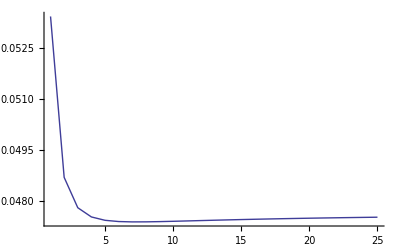

```mathematica
gr=PrintRange[Last/@linc]
```

```mathematica
If[!NumericQ[E],Remove[E]];
cutout=6;
ltest=Last/@Drop[linc,cutout];
{lnaλ,λ}=CoefficientList[Fit[Log[-dif[ltest]],{1,x},x],x];
a=-E^lnaλ/λ;Print[{a,λ}];
```

{-0.0057025-4.81507×10^-17 ⅈ,-0.00125945+9.67012×10^-18 ⅈ}

```mathematica
ListPlot[ltest-Table[a ⅇ^(λ x),{x,1,Length[ltest]}]]
```

```mathematica
{19.0075,0.0530871}
```

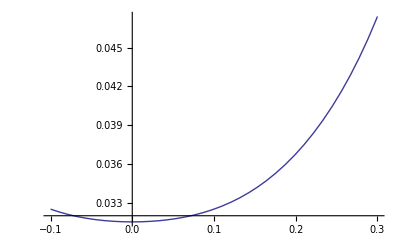

```mathematica
ShowPlot[GetMainIncrement[100,#,1000]&,{-0.1,0.3},All,PlotPoints->5,MaxRecursion->4]
```

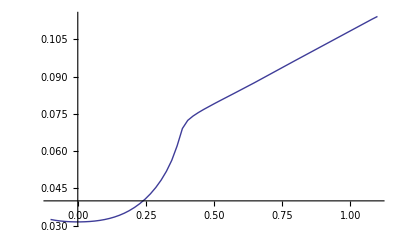

```mathematica
ShowPlot[GetMainIncrement[100,#,1000]&,{-0.1,1.1},All,PlotPoints->5,MaxRecursion->4]
```

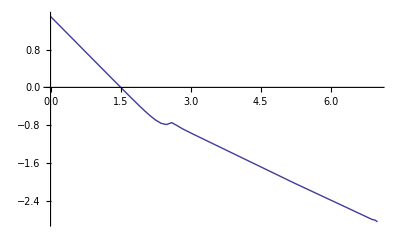

```mathematica
ShowPlot[Log[10,GetMainIncrement[100,1,10^#]]&,{0,7},All,PlotPoints->5,MaxRecursion->4]
```

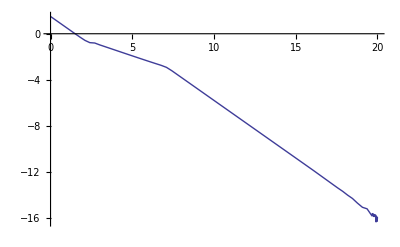

```mathematica
ShowPlot[Log[10,GetMainIncrement[100,1,10^#]]&,{0,20},All,PlotPoints->5,MaxRecursion->4]
```